# QLMS Rabi Process

## Last Updated: 08/06/2023

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

```mathematica
(*todo: create import dataset function that puts together all of "User Input" section*)
```

## General

## Values

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
```

### Fundamental

```mathematica
(*natural*)
ℏ=1.0545718*^-34;
c=2.99792458*^8;
```

```mathematica
(*statistical mechanics*)
kb=1.38064852*^-23;
```

```mathematica
(*electron units*)
me=9.10938356*^-31;
qe=1.60217662*^-19;
```

```mathematica
(*electromagnetism*)
ϵ0 = 8.8541878128*^-12;
μ0=π*4.*^-7;
```

```mathematica
(*atomic*)
amu=1.66053904*^-27;
```

### Derived

```mathematica
(*qe^2/(4 Subscript[πϵ, 0])*)
ke2=2.30707751*^-28;
```

```mathematica
(*fine structure constant*)
αfs=ke2/(ℏ*c);
```

```mathematica
(*bohr radius*)
a0=ℏ^2/(me*ke2);
```

```mathematica
(*bohr magneton*)
μB=(qe*ℏ)/(2*me);
```

```mathematica
(*debye*)
debye=(1.*^-21)/c;
```

### Units

```mathematica
(*frequency*)
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2.π*{10.^3,10.^6,10.^9};
```

```mathematica
(*time*)
{ns,μs,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
(*distance*)
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Evaluations

```mathematica
(*scde2={
Off[General::munfl],
Off[FindRoot::lstol],
Off[FindFit::cvmit],
Off[FindFit::sszero],
Off[FindFit::nrjnum],
Off[NonlinearModelFit::cvmit],
Off[NonlinearModelFit::sszero],
Off[Power::infy],
Off[Infinity::indet],
Off[FittedModel::constr]
};*)
```

```mathematica
(*Evaluate[#]&/@scde2*)
```

```mathematica
(*scde={
General::munfl,
FindRoot::lstol,
FindFit::cvmit,
FindFit::sszero,
FindFit::nrjnum,
NonlinearModelFit::cvmit,
NonlinearModelFit::sszero,
Power::infy,
Infinity::indet,
FittedModel::constr
};*)
```

```mathematica
(*Off[#]&/@scde*)
```

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
];
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
];
```

## Functions

### General

```mathematica
(*play sound when finished*)
Done[type_:"email",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}]},
Switch[type,
"text",SendMessage["SMS",msg],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->ToString[$MachineName],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Body"->msg,"Password"->"I2Ic1zIS2R"|>],"none",EmitSound[soundDJ]
];
];
```

### Dataset Processing

```mathematica
(*import already demodulated dataset*)
ProcessDataset[filename_]:=Module[
{
(*actual data*)
datasetRaw=Import[filename,{"/datasets/results"}],
(*parameters*)
(*modulationAmplitude=Import[filename,{"/datasets/modulation_amplitude_vpp"}],*)
(*processing*)
results,
carrierFreqMHz,
countThreshold
},

(*convert data to frequency, counts*)
results=Transpose[{
datasetRaw[[;;,1]]*ftwToFrequencyMHz,(*AOM/readout frequency, MHz*)
datasetRaw[[;;,4]]*1.*^-3,(*sideband frequency, kHz*)
datasetRaw[[;;,2]](*counts*)
}];

(*calculate values for processing*)
(*guess AOM/readout frequency*)
carrierFreqMHz=Mean[results[[;;,1]]];
(*find count threshold*)
countThreshold=FindThreshold[results[[;;,3]]];

(*process data*)
(*create copy of dataset and directly threshold counts into states*)
results[[;;,-1]]=1.-UnitStep[results[[;;,-1]]-countThreshold];
(*average states into probabilities*)
results=GroupBy[
results,
#[[;;2]]&,
N[Mean[#]]&
]//Values;

(*group by RSB/BSB*)
results=GroupBy[
results,
First[#]<carrierFreqMHz&
];
results={results[True],results[False]};
(*remove AOM/readout frequency and sort by x-axis*)
results=SortBy[#,First]&/@results[[;;,;;,2;;]];

(*clean up mess*)
Remove[datasetRaw];
ClearSystemCache[];

(*return dataset*)
Return[results];
];
```

### Phonon Conversion

```mathematica
coherentX0="0\t9.99968345065521e-05\t0.000399949359050543\t0.000899743688795304\t0.00159919018917467\t0.00249802373567682\t0.00359590407662662\t0.00489241629804741\t0.00638707138943964\t0.00807930690905264\t0.00996848774698177\t0.0120539069841832\t0.0143347868452619\t0.0168102797426638\t0.0194794694096749\t0.0223413721194334\t0.0253949379869404\t0.0286390523508750\t0.0320725372318338\t0.0356941528634366\t0.0395025992925868\t0.0434965180450157\t0.0476744938521131\t0.0520350564349007\t0.0565766823409077\t0.0612977968295938\t0.0661967758018701\t0.0712719477691913\t0.0765215958576296\t0.0819439598422616\t0.0875372382071775\t0.0932995902263676\t0.0992291380607130\t0.105323968866310\t0.111582136909319\t0.118001665682565\t0.124580550019086\t0.131316758197884\t0.138208234037120\t0.145252898970045\t0.152448654098991\t0.159793382222768\t0.167284949832890\t0.174921209074062\t0.182699999664427\t0.190619150771128\t0.198676482836768\t0.206869809352429\t0.215196938572920\t0.223655675170015\t0.232243821819463\t0.240959180717564\t0.249799555023207\t0.258762750221224\t0.267846575402984\t0.277048844460143\t0.286367377187489\t0.295800000290804\t0.305344548295672\t0.314998864353126\t0.324760800938008\t0.334628220435874\t0.344598995614207\t0.354671009973656\t0.364842157974930\t0.375110345136883\t0.385473488001222\t0.395929513959161\t0.406476360935198\t0.417111976923057\t0.427834319368674\t0.438641354394938\t0.449531055862707\t0.460501404262433\t0.471550385430509\t0.482675989084237\t0.493876207169105\t0.505149032011798\t0.516492454272143\t0.527904460686948\t0.539383031598436\t0.550926138259732\t0.562531739909640\t0.574197780608683\t0.585922185828196\t0.597702858784029\t0.609537676506275\t0.621424485636251\t0.633361097941900\t0.645345285542670\t0.657374775834950\t0.669447246109191\t0.681560317849959\t0.693711550710419\t0.705898436153020\t0.718118390748662\t0.730368749127130\t0.742646756572379\t0.754949561257081\t0.767274206112027\t0.779617620327223\t0.791976610483122";
coherentX0=Internal`StringToMReal/@StringSplit[coherentX0,"\t"];
```

```mathematica
coherentY0="0\t0.000100000000000000\t0.000400000000000000\t0.000900000000000000\t0.00160000000000000\t0.00250000000000000\t0.00360000000000000\t0.00490000000000000\t0.00640000000000000\t0.00810000000000000\t0.0100000000000000\t0.0121000000000000\t0.0144000000000000\t0.0169000000000000\t0.0196000000000000\t0.0225000000000000\t0.0256000000000000\t0.0289000000000000\t0.0324000000000000\t0.0361000000000000\t0.0400000000000000\t0.0441000000000000\t0.0484000000000000\t0.0529000000000000\t0.0576000000000000\t0.0625000000000000\t0.0676000000000000\t0.0729000000000000\t0.0784000000000000\t0.0841000000000000\t0.0900000000000000\t0.0961000000000000\t0.102400000000000\t0.108900000000000\t0.115600000000000\t0.122500000000000\t0.129600000000000\t0.136900000000000\t0.144400000000000\t0.152100000000000\t0.160000000000000\t0.168100000000000\t0.176400000000000\t0.184900000000000\t0.193600000000000\t0.202500000000000\t0.211600000000000\t0.220900000000000\t0.230400000000000\t0.240100000000000\t0.250000000000000\t0.260100000000000\t0.270400000000000\t0.280900000000000\t0.291600000000000\t0.302500000000000\t0.313600000000000\t0.324900000000000\t0.336400000000000\t0.348100000000000\t0.360000000000000\t0.372100000000000\t0.384400000000000\t0.396900000000000\t0.409600000000000\t0.422500000000000\t0.435600000000000\t0.448900000000000\t0.462400000000000\t0.476100000000000\t0.490000000000000\t0.504100000000000\t0.518400000000000\t0.532900000000000\t0.547600000000000\t0.562500000000000\t0.577600000000000\t0.592900000000000\t0.608400000000000\t0.624100000000000\t0.640000000000000\t0.656100000000000\t0.672400000000000\t0.688900000000000\t0.705600000000000\t0.722500000000000\t0.739600000000000\t0.756900000000000\t0.774400000000000\t0.792100000000000\t0.810000000000000\t0.828100000000000\t0.846400000000000\t0.864900000000000\t0.883600000000000\t0.902500000000000\t0.921600000000000\t0.940900000000000\t0.960400000000000\t0.980100000000000\t1\t1.02010000000000";
coherentY0=Internal`StringToMReal/@StringSplit[coherentY0,"\t"];
```

```mathematica
CoherentC=Interpolation[Transpose[{coherentX0,coherentY0}]];
```

## User Input

## Parameters

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2023-08-06";
(*directoryString="/Users/claytonho/Documents/Research/Data & Analysis/Calibrations";*)
(*directoryString="/Volumes/groups/motion/Data/2023-07-27";*)
```

```mathematica
(*select run*)
rid=26947;
```

## Process User Input

```mathematica
(*select file with give RID from all subdirectories*)
filenamesAll=FileNames["*.h5",directoryString,Infinity];
filenamesDJ=Select[filenamesAll,StringContainsQ[#,ToString[rid]]&];
```

```mathematica
(*just select dataset of interest as the first one that shows up that matches our RID*)
filenameDJ=First@filenamesDJ;
```

### Validate Input

```mathematica
(*check input directory exists*)
If[!DirectoryQ[directoryString],
MessageDialog["Failure :(\nError: Import directory not found ("<>directoryString<>")."];
FrontEndTokenExecute["EvaluatorAbort"];
];
```

```mathematica
(*check desired file exists*)
If[!FileExistsQ[filenameDJ],
MessageDialog["Failure :(\nError: Specified file not found ("<>filenameDJ<>")."];
FrontEndTokenExecute["EvaluatorAbort"]
];
```

```mathematica
(*(*check desired file is correct for processing*)
If[!StringContainsQ[filenamesDJ[[1]],"parametric",IgnoreCase->True],
MessageDialog["Failure :(\nError: Selected file incompatible with this Notebook.\nSelected file: "<>filenameDJ<>"."];
FrontEndTokenExecute["EvaluatorAbort"]
];*)
```

```mathematica
(*raise message dialog to let user know everything is OK*)
(*MessageDialog["Success!\nDesired file found: "<>filenameDJ];*)
```

## Process

## Preprocess

```mathematica
asfToPCT=100./Interpreter["HexInteger"]["3FFF"];
```

```mathematica
(*import and convert*)
ds=Import[filenameDJ,{"datasets/results"}];
ds=Transpose[{ds[[;;,1]],ds[[;;,3]],ds[[;;,2]]}];
ds[[;;,1]]*=ftwToFrequencyMHz;
ds[[;;,2]]*=ftwToFrequencyMHz*1000;
```

```mathematica
(*threshold*)
Histogram[ds[[;;,3]]];
thresh=FindThreshold[ds[[;;,3]]];
sc0=ds;
sc0[[;;,3]]=UnitStep[ds[[;;,3]]-thresh];
```

```mathematica
(*group and convert to probability*)
th0=GroupBy[
sc0,
#[[;;2]]&,
N[Mean[#[[;;,3]]]]&
];
th0=Transpose[Join[Transpose[Keys[th0]],{Values[th0]}]];
```

```mathematica
(*split rsb and bsb*)
carrierFreqMHz=(Min[ds[[;;,1]]]+Max[ds[[;;,1]]])/2.;
```

```mathematica
{thRSB,thBSB}=GatherBy[th0,First[#]<carrierFreqMHz&];
{thRSB,thBSB}=SortBy[#,First]&/@{thRSB,thBSB};
```

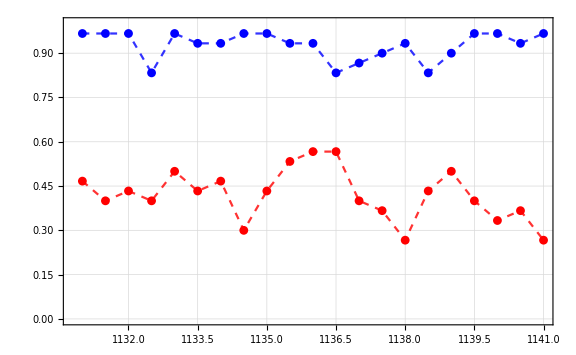

```mathematica
ListPlot[
{
thRSB[[;;,2;;]],
thBSB[[;;,2;;]],
thRSB[[;;,2;;]],
thBSB[[;;,2;;]]
},
PlotRange->{0.,1.},
Joined->{False,False,True,True},
PlotStyle->{{Red},{Blue},{Red,Dashed,Opacity[0.8]},{Blue,Dashed,Opacity[0.8]}}
]
```